```mathematica
Экзамен по Функциональному Программированию Чобану Артём I902
```

```mathematica
1.1 Откорректировать код и отметить вывод,соответствующий коду. Ответ: b
```

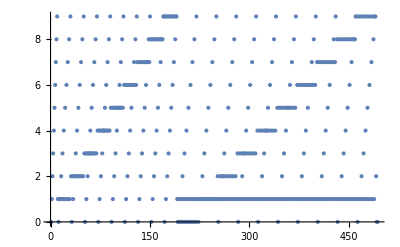

```mathematica
ListPlot[Flatten[IntegerDigits/@Range[0,200]]]
```

```mathematica
1.2 Отметить правильный результат. Ответ: b
```

```mathematica
u=Range[3];v=-u;u*v+3
```

{2,-1,-6}

```mathematica
1.3 Откорректировать код и сгенерировать результа.
```

```mathematica
Graphics[{White,Riffle[NestList[Scale[Rotate[#,0.1],0.9]&,RegularPolygon[6],40],{Pink,Yellow}]}]
```

-Graphics-

```mathematica
1.4 Описать основные принципы программирования,основанного на правилах и патернах,в
языке Вольфрам.Привести примеры.Используя соответствие патернов извлечь
отрицательные корни следующего уравнения:x^9+3.4 x^6-25 x^5-213 x^4-477 x^3+1012 x^2+111 x–123=0
```

```mathematica
Все корни(включая комплексные)
```

```mathematica
Solve[x^9+3.4 x^6-25 x^5-213 x^4-477 x^3+1012 x^2+111x-123 == 0, x]
```

{{x→-2.80961},{x→-1.85186-2.15082 ⅈ},{x→-1.85186+2.15082 ⅈ},{x→-0.376453},{x→0.323073},{x→1.06103-3.12709 ⅈ},{x→1.06103+3.12709 ⅈ},{x→1.30533},{x→3.13931}}

```mathematica
Только отрицательные:
```

```mathematica
Select[x /.Solve[x^9+3.4 x^6-25 x^5-213 x^4-477 x^3+1012 x^2+111x-123 == 0, x], Negative]
```

{-2.80961,-0.376453}

```mathematica
1.5 Откорректировать выражение и написать результат выполнения кода.
```

```mathematica
Cases[{3,4,x,x^2,x^3},x^n_->2 x]
```

{2 x,2 x}

```mathematica
2.1 Списки и их манипулирование. Записать результаты выполнения:
```

```mathematica
Table[Sin[n/7],{n,0,4}]
```

{0,Sin[1/7],Sin[2/7],Sin[3/7],Sin[4/7]}

```mathematica
Table[i^x+2 i,{i,5}]
```

{3,4+2^x,6+3^x,8+4^x,10+5^x}

```mathematica
m=Table[i-j,{i,3},{j,3}]
```

{{0,-1,-2},{1,0,-1},{2,1,0}}

```mathematica
m[[2]]
```

{1,0,-1}

```mathematica
2.2Функциональное программирование.Примитивы. Записать,также,результаты выполнения ячеек:
```

```mathematica
zz/@{1,{1},{1,2}}
```

{zz[1],zz[{1}],zz[{1,2}]}

```mathematica
zz@@{1,{1},{1,2}}
```

zz[1,{1},{1,2}]

```mathematica
zz@@@{1,{1},{1,2}}
```

{1,zz[1],zz[1,2]}

```mathematica
Fold[zz,0,{1,{1},{1,2}}]
```

zz[zz[zz[0,1],{1}],{1,2}]

```mathematica
FoldList[zz,0,{1,{1},{1,2}}]
```

{0,zz[0,1],zz[zz[0,1],{1}],zz[zz[zz[0,1],{1}],{1,2}]}

```mathematica
Nest[zz,{1,{1},{1,2}},3]
```

zz[zz[zz[{1,{1},{1,2}}]]]

```mathematica
2.3 Чистые функции
```

```mathematica
h[x_]:=f[x]+g[x]
```

```mathematica
Map[h,{a,b,c}]
```

{f[a]+g[a],f[b]+g[b],f[c]+g[c]}

```mathematica
Map[f[#]+g[#]&,{a,b,c}]
```

{f[a]+g[a],f[b]+g[b],f[c]+g[c]}

```mathematica
Map[f[#+g[#]]&,{a,b,c}]
```

{f[a+g[a]],f[b+g[b]],f[c+g[c]]}

```mathematica
3.1 Написать программу в языке Вольфрам которая определяет функцию,вычисляющую для
натурального аргумента n выражение 3^n,а также другую функцию,которая вычисляет для натурального аргумента 
n сумму 3^0 + 3^1+ ... + (3^n).Проиллюстрировать применение функций.
```

```mathematica
CountSum[n_] := Sum[3^i, {i, n}]
```

```mathematica
CountSum[1]
CountSum[2]
```

3

12

```mathematica
3.2 Операции над списками. Составить код для нахождения среди первых 100 натуральных чисел тех,которые являются одновременно квадратами и кубами некоторых из рассмотренных чисел. Привести код и результат его выполнения.
```

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
IsCube[x_] := IntegerQ[CubeRoot[x]]
IsSquare[x_] := IntegerQ[Sqrt[x]]

IsSuitable[x_] := IsSquare[x] && IsCube[x]
Select[Range[100],IsSuitable ]
```

{1,64}